## Require PerkelTheory.nb to run

```mathematica
data1=Import["data1a.mat"];
data2=Import["data2a.mat"];
data3=Import["data3a.mat"];
data3[[1, ;;, 1]]=0;
```

```mathematica
Mean/@data2[[;;, ;;, 1]]
```

{18.4533,1.42333,19.07,0.496667,0.923333,0.833333,0.553333,0.91,0.95,0.796667,1.07333,1.24333,1.42333,1.25333,0.81,0.32,0.626667,0.48,0.0133333,1.03667,0.78,20.26,0.753333,0.446667,0.956667,0.956667,0.536667,0.996667,0.863333,0.946667,0.536667,1.05667,0.41,0.44,0.616667,1.07,0.6,1.19,0.61,0.473333}

## Phase extraction and screening

```mathematica
filterPhase[data_, th_:π/24]:=Module[{avg=Mean@Mean@data[[;;, ;;, {2, 3}]], temp},
temp=Map[#-Join[{0}, avg]&, data, {2}];
Select[#, (Abs[#[[2]]]<th&&Abs[#[[3]]]<th&)]&/@temp
];
```

```mathematica
data1f=filterPhase[data1];
(Length/@data1f)//Min
data2f=filterPhase[data2];
(Length/@data2f)//Min
data3f=filterPhase[data3];
(Length/@data3f)//Min
```

12

24

6

```mathematica
Module[{th=π/24, avg=Mean@(Mean/@(Join[data1, data2, data3][[;;, ;;, {2, 3}]]))},
Graphics[{PointSize->.01, AbsoluteThickness[2], FontFamily->"Minion Pro", FontSize->28,
LightGray, Cuboid[{-.2, -.2}, {.2, .2}], 
White, Cuboid[{-th, -th}, {th, th}], 
Gray, Line[{{{-.2, -th}, {.2, -th}}, {{-.2, th}, {.2, th}}, {{-th, -.2}, {-th, .2}}, {{th, -.2}, {th, .2}}}], 
{Transparent, EdgeForm[{Black, AbsoluteThickness[2]}], Cuboid[{-.2, -.2}, {.2, .2}]},
Black, Table[Line[{{{k, -.199}, {k, -.196}}, {{-.199, k}, {-.196, k}}}], {k, -4π/72, 4π/72, π/144}],Table[Line[{{{k, -.199}, {k, -.192}}, {{-.199, k}, {-.192, k}}}], {k, -4π/72, 4π/72, π/36}],
If[Abs[#[[1]]]<.196&&Abs[#[[2]]]<.196, {If[Abs[#[[1]]]<th&&Abs[#[[2]]]<th, RGBColor[{0, 105, 169}/255], RGBColor[{243, 90, 93}/255]], Point[#]}, Null]&/@((#-avg)&/@Flatten[Join[data1, data2, data3][[;;, 7;;7, 2;;]], 1]), 
Text["Convolution phase / °", {-.27, 0}, {0, -1}, {0, 1}], 
Text["LO phase / °", {0, -.25}, {0, 1}, {1, 0}],
Table[Text[ToString[5k], {-.21, k π/36}, {1, 0}], {k, -2, 2}],
Table[Text[ToString[5k], {k π/36, -.20}, {0, 1}], {k, -2, 2}]
}, ImageSize->370]
]
```

-Graphics-

```mathematica
1/Degree*Mean@Flatten[(Join[data1, data2, data3][[;;, ;;, 2]])]
1/Degree*Mean@Flatten[(Join[data1, data2, data3][[;;, ;;, 3]])]
1/Degree*StandardDeviation@Flatten[(Join[data1, data2, data3][[;;, ;;, 2]])]
1/Degree*StandardDeviation@Flatten[(Join[data1, data2, data3][[;;, ;;, 3]])]
```

2.99357

4.46234

3.9358

2.73757

## Hardy-type paradox

```mathematica
hardyprob=((Total@(#^2)&@Take[#, 19])/(Total@(#^2)&@#))&@Part[(Mean/@data2f[[stateposlv2, ;;, 1]]), #]&/@{;;37, 38;;74, 75;;}
Total@hardyprob
```

{0.993895,0.998,0.998341}

2.99024

```mathematica
hardyterms=((#^2&@Take[#, 19])/(Total@(#^2)&@#))&@Part[(Mean/@data2f[[stateposlv2, ;;, 1]]), #]&/@{;;37, 38;;74, 75;;}
```

{{0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103,0.0523103},{0.052899,0.052899,0.052899,0.052899,0.052899,0.052899,0.052899,0.051129,0.051129,0.052899,0.052899,0.052899,0.052899,0.052899,0.051129,0.051129,0.052899,0.052899,0.052899},{0.056148,0.056148,0.056148,0.0485401,0.0485401,0.0485401,0.056148,0.056148,0.056148,0.056148,0.0485401,0.0485401,0.056148,0.056148,0.056148,0.0485401,0.0485401,0.0485401,0.0485401}}

## Violation of NCHV inequality

```mathematica
estnorm=Total@(Mean/@data2f[[stateposlv2, ;;, 1]])/57;
penalty=Total[(#/estnorm)^2&/@Total/@Map[Mean, (data3f[[#, ;;, 1]])&/@errpos, {2}]]/19/2
Total@hardyprob-penalty
```

0.65094

2.3393

```mathematica
({0.650940342556335, 0.040063858396451185}*19*2)/EdgeCount[GraphComplement@GraphData["PerkelGraph"]]
```

{0.0173584,0.00106837}

## Bootstrapping for error estimation

```mathematica
hardyerr=Module[{j, rand={}, seq},
SeedRandom[8023]; 
For[j=1, j≤200, j++, 
seq=RandomSample[#, 20]&/@data2f;
AppendTo[rand, ((Total@(#^2)&@Take[#, 19])/(Total@(#^2)&@#))&@Part[(Mean/@seq[[stateposlv2, ;;, 1]]), #]&/@{;;37, 38;;74, 75;;}]];
StandardDeviation@rand
]
```

{0.00159083,0.0002539,0.000202713}

```mathematica
penaltyerr=Module[{j, rand={}, seq}, 
SeedRandom[8023];
For[j=1, j≤200, j++, 
seq=RandomSample[#, Min[Length@#, 9]]&/@data3f;
AppendTo[rand, Total[(#/estnorm)^2&/@Total/@Map[Mean, (seq[[#, ;;, 1]])&/@errpos, {2}]]/19/2]];
StandardDeviation@rand
]
```

0.0400639

```mathematica
Total@hardyerr+penaltyerr
(Total@hardyprob-penalty-2)/(Total@hardyerr+penaltyerr)
```

0.0421113

8.05712

## Amplitude correction for LV2 vectors

```mathematica
prlv1new=Module[{dataq=Part[(Mean/@data1f[[;;, ;;, 1]]), #]&/@stateposlv1},
dataq[[;;, 4;;]]=0; 
Flatten[#, 1]&@((Part[dataq, #]&/@{;;37, 38;;74, 75;;})/(√(Total/@(#^2&/@Part[dataq//Flatten, #]&/@{;;222, 223;;444, 445;;}))))
];
```

```mathematica
Correlation[Total/@prlv1new,  Total/@prlv1]
```

0.995771

## Plots

```mathematica
ColorData[51, #]&/@Table[k, {k, 8}]
ColorData[55, #]&/@Table[k, {k, 2, 9}]
ColorData[75, #]&/@Table[k, {k, 8}]
```

{RGBColor[1, 0.753262, 0.0437629],RGBColor[0.945708, 0.661402, 0.128328],RGBColor[1, 0.854948, 0.112474],RGBColor[0.850675, 0.561089, 0.0324254],RGBColor[1, 0.70927, 0.144472],RGBColor[0.714931, 0.467216, 0.0763714],RGBColor[1, 0.79234, 0.292164],RGBColor[0.592767, 0.410986, 0.121248]}

{RGBColor[0.813855, 0.974746, 0.996429],RGBColor[0.76527, 0.954757, 0.912932],RGBColor[0.581781, 0.801038, 0.828061],RGBColor[0.66154, 0.87277, 0.882353],RGBColor[0.616999, 0.753475, 0.909499],RGBColor[0.88957, 0.713878, 1],RGBColor[0.737484, 0.745327, 0.909499],RGBColor[0.775662, 0.632776, 0.918547]}

{Hue[0.22, 1, 0.51],Hue[0.21, 0.8, 0.85],Hue[0.28, 0.75, 0.6],Hue[0.25, 1, 0.85],Hue[0.45, 1, 0.55],Hue[0.22, 1, 0.68],Hue[0.3, 1, 0.51],Hue[0.28, 0.6, 0.85]}

```mathematica
With[{h=.23, stack={0, hardyprob[[1]], hardyprob[[1]]+hardyprob[[2]]}+(PadLeft[#, 20]&/@Accumulate/@hardyterms)},
Graphics[{EdgeForm[None], AbsoluteThickness[2], CapForm["Round"], JoinForm["Round"], FontSize->20, FontFamily->"Minion Pro",
LightGray, Cuboid[{0, -.1}, {2, .25+h}],
Table[{ColorData[75, Mod[k-1, 8]+1], Cuboid[{stack[[1, k]], 0}, {stack[[1, k+1]], h}]}, {k, 19}], 
Table[{ColorData[55, Mod[k+2, 6]+1], Cuboid[{stack[[2, k]], 0}, {stack[[2, k+1]], h}]}, {k, 19}], 
Table[{ColorData[51, Mod[k-1, 8]+1], Cuboid[{stack[[3, k]], 0}, {stack[[3, k+1]], h}]}, {k, 19}],
Gray, {Dashing[{.02, .02}], Line[{{2, -.1}, {2, .25+h}}]},
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{0, -.1}, {3, .25+h}]},
Red,Line[{{{Total@hardyprob-Total@hardyerr-penaltyerr, h/2}, {Total@hardyprob+Total@hardyerr+penaltyerr, h/2}}, {{Total@hardyprob-Total@hardyerr-penaltyerr, h/2-.08}, {Total@hardyprob-Total@hardyerr-penaltyerr, h/2+.08}}, {{Total@hardyprob+Total@hardyerr+penaltyerr, h/2-.08}, {Total@hardyprob+Total@hardyerr+penaltyerr, h/2+.08}}}],
Hue[0, 0, 0.1], Cuboid[{1.98, h+.08}, {2.02, h+.18}], Arrow[Line[{{2, h+.13}, {1.7, h+.13}}]], Text["NCHV", {1.48, h+.13}],
Blend[{RGBColor[{73, 48, 146}/255], White}], {Dashing[{.02, .02}], Line[{{2+penalty, -.1}, {2+penalty, .25+h}}]}, Line[{{2+penalty, .38+h}, {2+penalty, .2+h}}],
RGBColor[{73, 48, 146}/255], Cuboid[{1.98+penalty, h+.32}, {2.02+penalty, h+.42}], Arrow[Line[{{2+penalty, h+.37}, {1.7+penalty, h+.37}}]], Text["Exclusivity-corrected NCHV", {0.9+penalty, h+.37}],
Black, Text["Q_max", {3, h+.37}], Text[ToString@#, {#, -.2}]&/@{0, 2, 3}
}, ImageSize->480]]
```

-Graphics-

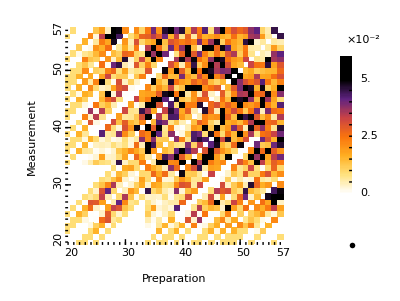

```mathematica
With[{err=(#/estnorm)^2&/@Total/@Map[Mean, (data3f[[#, ;;, 1]])&/@errpos, {2}], orthoreduced=Map[If[#≤19, 0, #-19]&, Position[gmat, 0], {2}]}, 
Graphics[{EdgeForm[None], AbsoluteThickness[2], CapForm["Round"], JoinForm["Round"], FontSize->20, FontFamily->"Minion Pro",
Table[{ColorData["SunsetColors"][1-err[[k]]/0.05], Cuboid[{orthoreduced[[k, 1]]-1, orthoreduced[[k, 2]]-1}, {orthoreduced[[k, 1]], orthoreduced[[k, 2]]}]}, {k, 2850}],
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{0, 0}, {38, 38}]},
AbsoluteThickness[1], Table[Line[{{k-.5, 0}, {k-.5, .5}}], {k, 38}], Table[Line[{{k-.5, 0}, {k-.5, 1}}], {k, 11, 31, 10}], 
Table[Line[{{0, k-.5}, {.5, k-.5}}], {k, 38}], 
Table[Line[{{0, k-.5}, {1, k-.5}}], {k, 11, 31, 10}],
Text["Preparation", {19, -5}, {0, 1}], Text["Measurement", {-5, 19}, {0, -1}, {0, 1}],
Text[ToString@#, {#-19, -.5}, {0, 1}]&/@{20, 30, 40, 50, 57},
Text[ToString@#, {-.3, #-19}, {0, -1}, {0, 1}]&/@{20, 30, 40, 50, 57}, 

Text["×10^-2", {52, 35}, {0, -1}],
{Table[{ColorData["SunsetColors"][1-(k-1)/99], Cuboid[{48, 8.8+.2k}, {50, 9+.2k}]}, {k, 120}]},
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{48, 9}, {50, 33}]},
Table[Line[{{50, 9+2k}, {49.5, 9+2k}}], {k, 9}], Text[ToString@#, {51.5, 9+4#}, {-1, 0}]&/@{0.0, 2.5, 5.0},
Text[Magnify[MaTeX["\\square = \\, \\not\\perp"], 0.8], {50, 0}]
}, ImageSize->400]]
```

## Detector response

```mathematica
pwr={0.0721, 0.320, 0.602, 0.916, 1.266, 1.655, 1.873, 2.100, 2.329, 2.563, 2.815, 3.050, 3.306, 3.560, 3.824, 4.090, 4.363, 4.643, 4.930, 5.17, 5.45, 5.74, 6.04, 6.33, 6.63, 6.92, 7.22, 7.54};
volt={18.6,96.5,186.,281.4,397.7,520.9,587.2,651.2,730.2,808.1,874.4,954.7,1028.,1106.,1187.,1264.,1340.,1426.,1506.,1578.,1657.,1717.,1750.,1795.,1820.,1833.,1840.,1850.};
```

```mathematica
Fit[{pwr[[;;20]], volt[[;;20]]}ᵀ, {1, x}, x]
```

7.76703+306.594 x

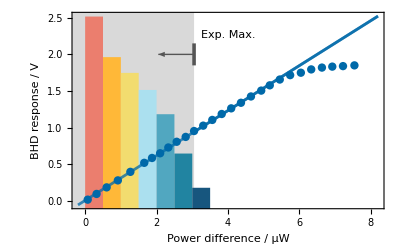

```mathematica
Show[
(*dummy*)
Plot[0.007767027518670593+0.3065939863832945 x, {x, -.2, 8.2}, PlotStyle->{RGBColor[{0, 105, 169, 192}/255], AbsoluteThickness[2]}, 

FrameLabel->{"Power difference / μW", "BHD response / V", None, Rotate["Events registered", π]},
FrameTicks->{{Automatic, {{0, "1"}, {0.6, "10"}, {1.2, "10^2"}, {1.8, "10^3"}, {2.4, "10^4"}}}, {Automatic, None}},
FrameStyle->Directive[{Black, FontFamily->"Minion Pro", FontSize->20}], Frame->True, ImageSize->400

], 
(*content*)
Graphics[{FontSize->20, FontFamily->"Minion Pro",
LightGray, Cuboid[{-1, -1}, {3.05, 3}], Darker@Gray, Cuboid[{3.0, 1.85}, {3.1, 2.15}], Arrowheads[.05], Arrow[Line[{{3.05, 2}, {2.05, 2}}]],
Table[{ColorData[24, k], Cuboid[{.5k-.5, -1}, {.5k, .6*Log10@BinCounts[Abs[Join[data1[[;;, ;;, 1]], data2[[;;, ;;, 1]], data3[[;;, ;;, 1]]]//Flatten]/10, {0, 3.5, .5}][[k]]}]}, {k, 7}],
Black, Text["Exp. Max.", {3.25, 2.2}, {-1, -1}]
}],
ListPlot[Transpose[{pwr, volt/1000}], PlotStyle->{RGBColor[{0, 105, 169}/255], AbsolutePointSize[6]}],
Plot[0.007767027518670593+0.3065939863832945 x, {x, -.2, 8.2}, PlotStyle->{RGBColor[{0, 105, 169, 192}/255], AbsoluteThickness[2]} 
]]
```

```mathematica
180/7.5
```

24.